# Retrospective evaluation of school-related measures on pre-vaccination transmission dynamics of SARS-CoV-2

## Benedetta Canfora, Rey Audie Escosio, Christiaan H. van Dorp, Otilia Boldea, Marc Bonten, Ana Nunes, and Ganna Rozhnova* Corresponding author: g.rozhnova@umcutrecht.nl

## Sensitivity analysis on fitting seroprevalence to tsero = 117

## Global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### Packages and parameters

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plotting`"];
Needs["preliminaries`"];

createResultDirectories[];

(*Remove["plotting`*"]
Get["../packages/plotting.m"]*)

(* Notebook parameters *)
ifShowFigs= True;
ifExportData = False;
ifExportFigs = False;
exportFormat={".pdf",".eps"};

(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 1000; (*Sensitivity for seroprevalence at 1000*)
stepSamples=20; (* Sens4sero is 10; 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

(* Scenarios *)
scenarios={"Baseline_117", "Scenario1_117", "Scenario2_117"};
numScenarios = Length[scenarios];
```

### Important dates and time step

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)


(* Integration end-time and time step *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(* Scenario time points *)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### Seroprevalence data

```mathematica
totalMeanSero=2.9;
totalLowMeanSero=2.0;
totalHighMeanSero=4.2;
seroTotalDataAround = Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}];

seroprevalenceData=100 * Drop[Import["../data/PT_SEROPREVALENCE_DATA.csv"],1][[All,5;;7]];
seroAgeDataAround=Table[Around[seroprevalenceData[[i,1]],{seroprevalenceData[[i,1]] - seroprevalenceData[[i,2]],seroprevalenceData[[i,3]] - seroprevalenceData[[i,1]]}],{i,1,Length[seroprevalenceData]}];

seroDataMay28Around =Flatten[ {seroTotalDataAround, seroAgeDataAround}];
```

### Contact matrices from Vespignani et al.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolContactDataBefore85=  11.41 * Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
```

### Transforming the contact matrices from 86x86 to 10x10

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];
contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
fileContactBefore10="../data/RES_PT_CONTACT_MATRIX_BEFORE_10.csv";
fileContactAfter10="../data/RES_PT_CONTACT_MATRIX_AFTER_10.csv";
fileSchoolBefore10="../data/RES_PT_CONTACT_MATRIX_SCHOOL_10.csv";
If[FileExistsQ[fileContactBefore10]&&FileExistsQ[fileContactAfter10]&&FileExistsQ[fileSchoolBefore10],

contactDataBefore10=Import[fileContactBefore10, "Table","FieldSeparators"->"\t"];
contactDataAfter10=Import[fileContactAfter10, "Table","FieldSeparators"->"\t"];
schoolContactDataBefore10=Import[fileSchoolBefore10, "Table","FieldSeparators"->"\t"];
,

contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];

Export[fileContactBefore10,contactDataBefore10, ];
Export[fileContactAfter10,contactDataAfter10];
Export[fileSchoolBefore10,schoolContactDataBefore10];
]

(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
```

## Hospitalization data and estimated parameters

### Estimated parameters

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES_SERO_117.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];
```

```mathematica
(* Total population *)
totalPop=Table[Subscript[NN,k]->demographyData10[[k]],{k,listAgeGroups}];

(* Contact matrix variables *)
contactRates=Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10[[k,l]],Subscript[a,{k,l}]->contactDataAfter10[[k,l]],Subscript[s,{k,l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];

(* Table for all parameters; also assigning variables *)
parametersComplete[sample_Integer]:=
Module[{est},
est=estimatesData[[sample]];
Flatten[{contactRates,totalPop,
(* Age-independent parameters *)
ϵ->est[[1]],ζ->est[[2]],α->est[[18]],γ->est[[19]],
(* Hospitalization rate *)
Table[Subscript[ν,k]->est[[2+k]],{k,1,numAgeGroups}],(* Initial conditions *)Table[{Subscript[S0,k]->1-est[[13]],Subscript[EE0,k]->0.5*est[[13]],Subscript[II0,k]->0.5*est[[13]],Subscript[R0,k]->0,Subscript[H0,k]->0},{k,listAgeGroups}],
(* Susceptibility *)
Table[Subscript[β,k]->est[[14]],{k,1,3}],Table[Subscript[β,k]->est[[15]],{k,4,7}],Table[Subscript[β,k]->est[[16]],{k,8,10}],
(* Logistic function parameters *){Subscript[xx,0]->est[[20]],Subscript[K,0]->est[[21]],Subscript[xx,1]->est[[22]],Subscript[K,1]->est[[23]],Subscript[xx,2]->est[[24]],Subscript[K,2]->est[[25]],Subscript[xx,3]->est[[26]],Subscript[K,3]->est[[27]],Subscript[xx,4]->est[[28]],Subscript[K,4]->est[[29]]},
{Subscript[u,1]->est[[30]],Subscript[u,2]->est[[31]],Subscript[u,3]->est[[32]],Subscript[u,4]->est[[33]]}}]];

(* Sampled parameters *)
parametersCompleteSampled=Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];
```

### Hospitalization data

```mathematica
(* Importing data *)
hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};


(* Transition dates and their respective quantiles *)transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
```

## Equations and variables

### Expressions for contact matrices

```mathematica
contactMatrixBaseline[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 1 *)
(* Schools remained open during LD1 before transitioning to the first relaxation of measures *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 2 *)
(* Schools remained closed after the 2020 summer holidays spanning Relax 2, LD 2, and Relax 3 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-Subscript[u, 4] Subscript[s,{k,l}]);
```

### Model equations

```mathematica
(* Table of equations *)Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];
NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];
```

```mathematica
(* The contact matrix to use *)
contactMatrix["Baseline",t_]:=contactMatrixBaseline[t];
contactMatrix["Scenario1",t_]:=contactMatrixScenario1[t];
contactMatrix["Scenario2",t_]:=contactMatrixScenario2[t];
contactMatrix["Scenario1_StrictLD",t_]:=contactMatrixScenario1StrictLD[t];
contactMatrix["Scenario1_ExtendSchools",t_]:=contactMatrixScenario1ExtendSchools[t];
contactMatrix["Scenario2_WinterHolidays",t_]:=contactMatrixScenario2WinterHolidays[t];
contactMatrix["Scenario2_AltReductions",t_]:=contactMatrixScenario2AltReductions[t];
contactMatrix[_,_]:=$Failed; (* Fallback error catch *)
```

```mathematica
(* Final table of equations considering the interventions as the argument *)
eqsList[intervention_String]:=
Module[{lambda},
(* Force of infection *)
lambda[k_,t_]:=ϵ*Sum[contactMatrix[intervention,t]*Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}];

Flatten[{
Table[Subscript[S,k]'[t]==-lambda[k,t]*Subscript[β,k]*Subscript[S,k][t],{k,listAgeGroups}],
Table[Subscript[EE,k]'[t]==lambda[k,t]*Subscript[β,k]*Subscript[S,k][t]-α*Subscript[EE,k][t],{k,listAgeGroups}],Table[Subscript[II,k]'[t]==α*Subscript[EE,k][t]-(γ+Subscript[ν,k])*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[R,k]'[t]==γ*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[H,k]'[t]==Subscript[ν,k]*Subscript[II,k][t],{k,listAgeGroups}]}]]
```

### Variables

```mathematica
(* List of variables for each compartment and their totals *)
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

(* Indices of the compartments in all of the equations (will come in handy in NGM) *)
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

(* Expression for the daily hospitalizations*)
hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
```

### Solving the model

```mathematica
(* Initial conditions *)
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];
(* Particularly for the compartments wherein we initially defined them as percentages from the total population (since N is constant through time)*)Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];

(* Function solving the model *)
solution[intervention_,pars_]:=NDSolve[Join[eqsList[intervention],ICsList]/.pars,
varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
(* and a for loop for each sample to solve it (this is still a function!) *)
solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
(* and finally importing/exporting them *)
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions/seroprevalence"];
```

```mathematica
(* We aim to evaluate these solutions of the model with respect to certain trajectories (hospitalizations and susceptible population for seroprevalence) *)
trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,tStep}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions/seroprevalence"]];

(* and since we will regroup them according to age-specific or total populations, we need to sum them accordingly *)
summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];
```

## Analysis

### Hospitalizations

```mathematica
(* Hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];

(* Simulating a negative binomial distribution, we regenerate the hospitalizations *)
NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions/seroprevalence"]];

(* Getting simulated (noised) hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPNEGBIN"];
hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

```mathematica
(* Plotting *)
(* Scatter plot for the hospitalization data *)scatterPlotHospData = DateListPlot[Total[hospitalizationData,{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];
scatterPlotHospDataChild = DateListPlot[Total[hospitalizationData[[All, 1;;3]],{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

(* For hospitalizations, we use the median of the solutions (not noised) and the quantiles of the simulated (noised) *)hospSimulTotal2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]],
hospitalizationSimulatedScenariosTotal[[2,1, All, All]],
hospitalizationSimulatedScenariosTotal[[3,1, All, All]]};
hospTot2Plot = {hospitalizationScenariosTotal[[1,1, All, All]],
hospitalizationScenariosTotal[[2,1, All, All]],
hospitalizationScenariosTotal[[3,1, All, All]]};
hospSimulYouth2Plot = {hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[3,1, All, All]]};
hospYouth2Plot={hospitalizationScenariosGrouped[[1,1, All, All]],
hospitalizationScenariosGrouped[[2,1, All, All]],
hospitalizationScenariosGrouped[[3,1, All, All]]};

figHospTotal = plotScenarioTrajectories[hospSimulTotal2Plot, "Total hospitalizations (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,590},{0,360}},{"a", "c"}, "lefter",scatterPlotHospData, 
hospTot2Plot];
figHospYouth = plotScenarioTrajectories[hospSimulYouth2Plot, "Youth hospitalizations (1/day)",{"", ""},{ticksVisible, ticksVisible},{{0,30},{0,10}},{"b", "d"}, "lefter",scatterPlotHospDataChild, 
hospYouth2Plot, False, "hosp"];


figHospTotalYouth = Grid[{{figHospTotal}, {figHospYouth}}];
```

### Seroprevalence

```mathematica
(* Susceptible population for the 10 age groups, for youth and adults, and for the total population *)susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];

(* Calculating the seroprevalence for the total population *)
seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];
(* for youth and adults *)
seroprevalenceScenariosGrouped = ConstantArray[0, {3,2,numSamples,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];
(* and for the 10 age groups *)
seroprevalenceScenarios = ConstantArray[0, {3,10,numSamples,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

```mathematica
(* Assuming that the susceptible population is proportional to the total population, the [1,5) population percentage can be computed as follows *)susceptible1to5Percent = Total[demographyData85[[2;;5]]]/Total[demographyData85[[1;;5]]];
susceptibleScenariosWithoutBabies = susceptibleScenarios;
susceptibleScenariosWithoutBabies[[All,1,All,All]]=susceptible1to5Percent*susceptibleScenarios[[All,1,All,All]];
demographyData10WithoutBabies = demographyData10;
demographyData10WithoutBabies[[1]] =susceptible1to5Percent* demographyData10[[1]];

regroupIndex = {{1,2}, {3},{4,5}, {6,7}, {8,9,10}};
susceptibleScenariosRegrouped = summingGroups4Scenarios[susceptibleScenariosWithoutBabies,regroupIndex ];
seroprevalenceScenariosRegrouped = ConstantArray[0, {3,5,numSamples,327}];
Table[seroprevalenceScenariosRegrouped[[All, k, All, All]]=
100-100susceptibleScenariosRegrouped[[All,k,All,All]]/Total[demographyData10WithoutBabies[[regroupIndex[[k]]]]];, {k ,1,5}];
```

### Infections

```mathematica
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
```

```mathematica
incidCumu = Transpose[Accumulate[Transpose[Total[incidencesScenarios, {2}],{2,3,1} ]], {3,1,2}];
Print[Median[incidCumu[[1,All,93]]]]
Print[Quantile[incidCumu[[1,All,93]],0.025]]
Print[Quantile[incidCumu[[1,All,93]],0.975]]
```

319662.

252005.

361634.

### Contacts

```mathematica
(* Evaluating the contact expressions *)
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrix[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];
importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions/seroprevalence"]];
(* and saving them as CONTACT files (these are still contact matrices) *)
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
(* Getting the average contacts *)
gettingAverageContacts[startrange_, endrange_] := 
Module[{summedRows,specificAges,demographyPercentage},
summedRows = Total[contactMatricesScenarios, {5}];
specificAges = summedRows[[All,All,All,startrange;;endrange]];
demographyPercentage =demographyData10[[startrange;;endrange]] / Total[demographyData10[[startrange;;endrange]]];
result=specificAges;
Do[result[[i,j,k,All]]=specificAges[[i,j,k,All]]*demographyPercentage,{i,1,numScenarios},{j,1,numSamples},{k,1,numTimes}];
result = Total[result, {4}];
result
];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal= gettingAverageContacts[1,10];
averageContactsYouth= gettingAverageContacts[1,3];
averageContactsAdults =gettingAverageContacts[4,10];
```

### Reproduction number

```mathematica
(* The next generation matrix for each scenario *)NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];

(* Substituting values to the next generation matrices *)
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;
NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop, "analysis/seroprevalence"];
```

```mathematica
(* Obtaining the reproduction number and the respective eigenvectors *)
eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop, "analysis/seroprevalence"];
```

### Cumulative elasticities

```mathematica
(* The remaining analyses are done numerically (and not symbolically) *)
(* Sensitivity matrices *)
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];
sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop, "analysis/seroprevalence"];

(* Elasticity matrices *)
elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop, "analysis/seroprevalence"];

(* Cumulative elasticities *)
cumuElasMatrix[elas_] :=
Total[elas,{1}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop, "analysis/seroprevalence"];

(* Adding cumulative elasticities for age-specific groups (youth and adults) *)
cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

```mathematica
(* Plotting *)
Rt1Line = Graphics[{Dashed,Black,InfiniteLine[{AbsoluteTime["February 26, 2020"],1},{AbsoluteTime["January 15, 2020"],1}]}];

Rt2Plot ={RtScenarios[[1,All,All,1]],
RtScenarios[[2,All,All,1]],
RtScenarios[[3,All,All,1]]};
cumuElas2Plot = {cumuElasGroupedScenarios[[1,All,All,1]],
cumuElasGroupedScenarios[[2,All,All,1]],
cumuElasGroupedScenarios[[3,All,All,1]]};

figRt = plotScenarioTrajectories[Rt2Plot, "Reproduction number",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,2.5},{0.8,1.4}}, {"a", "c"}, "righter", Rt1Line];
figCumuElas = plotScenarioTrajectories[cumuElas2Plot,"Cumulative youth elasticities",{"",""},{ticksVisible,ticksVisible},{{0,1},{0, 0.3}},{"b", "d"}, "righter", Graphics[], {{},{},{}}, False, "elas"];

figRtCumuElasChild = Grid[{{figRt}, {figCumuElas}}];
```

```mathematica
baseline4Sens2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]], hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosTotal[[1,1, All, All]],seroprevalenceScenariosGrouped[[1,1, All, All]],RtScenarios[[1,All,All,1]],cumuElasGroupedScenarios[[1,All,All,1]],averageContactsTotal[[1,All,All]],averageContactsYouth[[1,All,All]]};

measuresScenarios4Sens2Plot[scenarioIndex_] := {hospitalizationSimulatedScenariosTotal[[scenarioIndex+1,1, All, All]], hospitalizationSimulatedScenariosGrouped[[scenarioIndex+1,1, All, All]],
seroprevalenceScenariosTotal[[scenarioIndex+1,1, All, All]],seroprevalenceScenariosGrouped[[scenarioIndex+1,1, All, All]],RtScenarios[[scenarioIndex+1,All,All,1]],cumuElasGroupedScenarios[[scenarioIndex+1,All,All,1]],averageContactsTotal[[scenarioIndex+1,All,All]],averageContactsYouth[[scenarioIndex+1,All,All]]};
```

```mathematica
yLabel4SensShorter={"Total hosp. (1/day)","Youth hosp. (1/day)","Total sero. (%)","Youth sero. (%)","Rep. number","Cumu. youth elast.","Total cont. (1/day)","Youth cont. (1/day)"};

scenarioBaseIndices = {1,2};
scenarioMaxRanges =  ConstantArray[0, {2,2,2}];
scenarioMaxRanges[[1]] = {{0,630},{0,25},{0,30}, {0,30},{0,3},{0,0.9},{0,13},{0,17}};
scenarioMaxRanges[[2]] = {{0,360},{0,10},{0,30}, {0,30},{0.8,1.35},{0,0.29},{0,13},{0,17}};

scenarioTitles = {"Scenario 1 for ","Scenario 2 for "};

figGrid4Sens[scenarioIndex_] :=Module[{figList},
figList = Table[
plotWithLetter[{
plotLineWithCrI[Re[baseline4Sens2Plot[[m]]],colorBlue,"","",yLabel4SensShorter[[m]],scenarioBaseIndices[[scenarioIndex]],If[m <=4,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.75,250,Solid,Which[m == 1,hospitalizationScenariosTotal[[1,1,All,All]],
m == 2, hospitalizationScenariosGrouped[[1,1,All,All]],
True, {}], False,None],

plotLineWithCrI[Re[measuresScenarios4Sens2Plot[scenarioIndex][[m]]],colorOrange,"","","",scenarioBaseIndices[[scenarioIndex]],If[m <7,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.5,500,Solid,Which[m == 1,hospitalizationScenariosTotal[[scenarioIndex+1,1,All,All]],
m == 2, hospitalizationScenariosGrouped[[scenarioIndex+1,1,All,All]],
True, {}], False,None],

Which[m == 1,scatterPlotHospData,
m == 2, scatterPlotHospDataChild,
m == 5, Rt1Line,
True, Graphics[]]
},
alphabetLetters[[m]],"lefter"],
{m, 1, Length[yLabel4SensShorter]}];
figGrid = Grid[ArrayReshape[figList, {2,4}]];
figGrid = Grid[{{Style[scenarioTitles[[scenarioIndex]],TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{figGrid}, {Which[scenarioBaseIndices[[scenarioIndex]]==1, legendRawScen1HospFlat,scenarioBaseIndices[[scenarioIndex]]==2,legendRawScen2HospFlat]}}]];
```

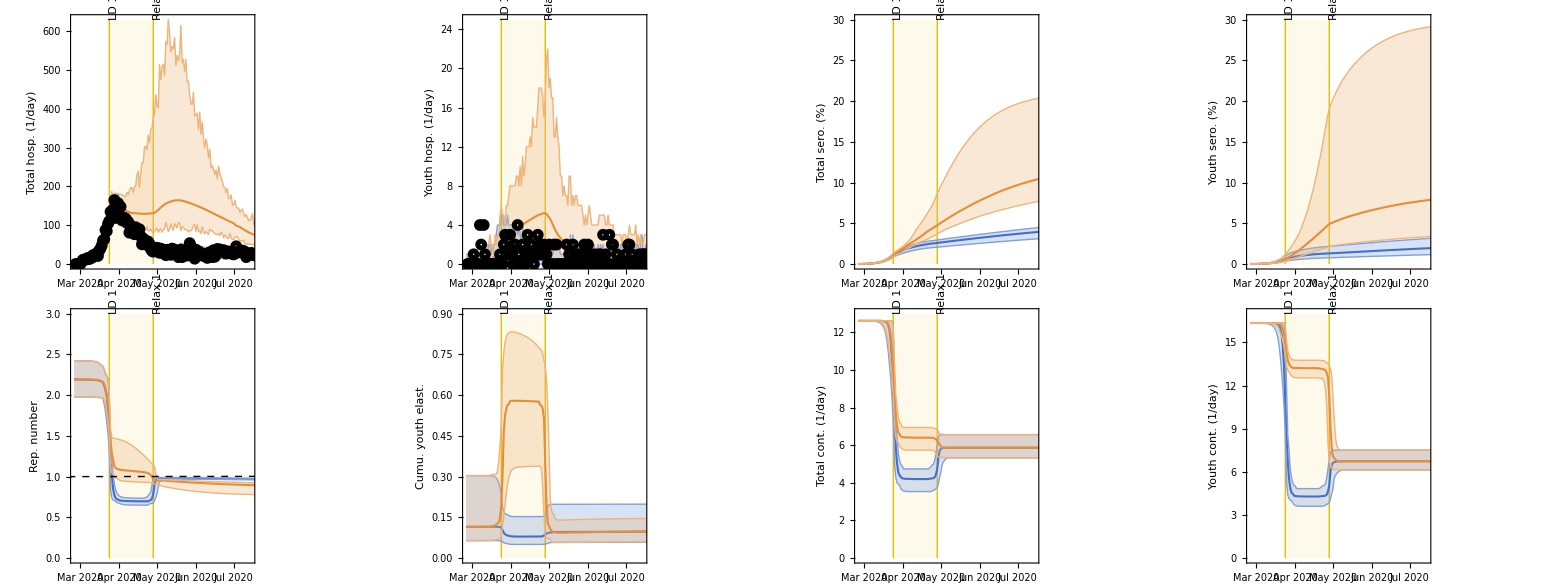
Scenario 1 for 
-Graphics-

```mathematica
exportFigs[figGrid4Sens[1],"SFig27"];
```

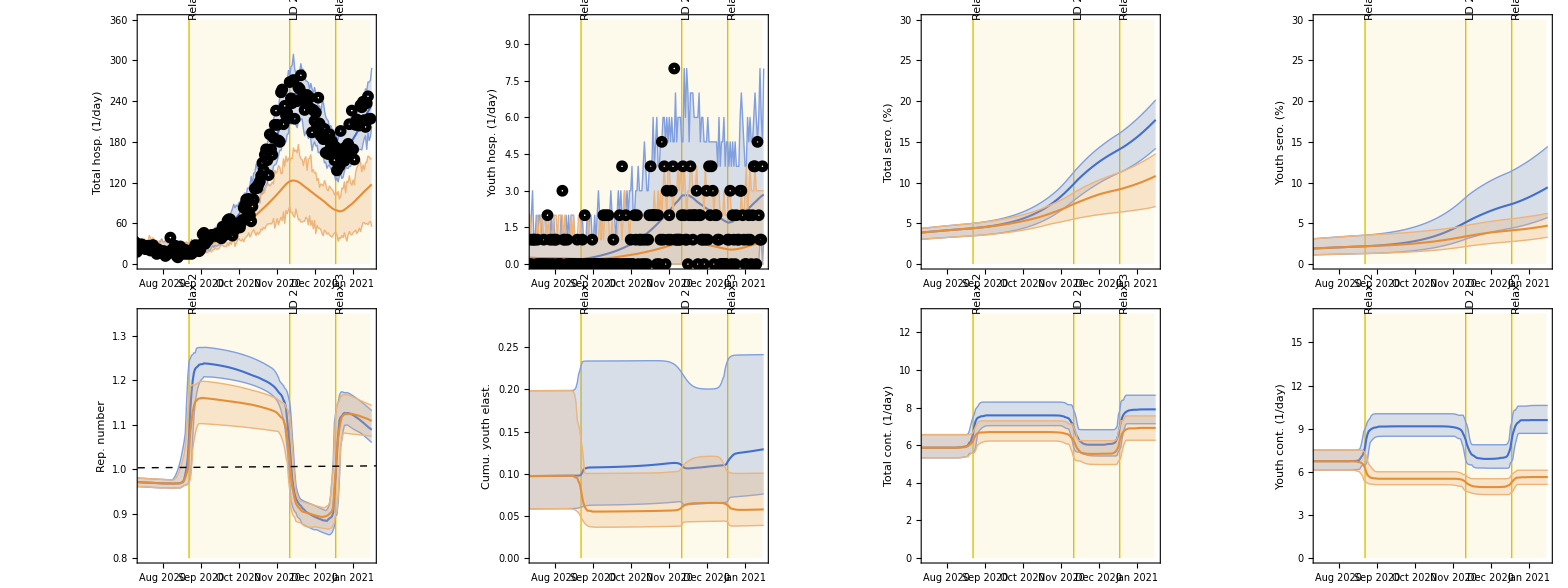
Scenario 2 for 
-Graphics-

```mathematica
exportFigs[figGrid4Sens[2],"SFig28"];
```

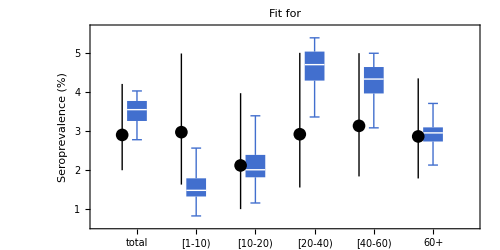

```mathematica
(* Plotting *)
seroEstimatesMay28 = {seroprevalenceScenariosTotal[[1,1,All,117]],seroprevalenceScenariosRegrouped[[1, 1, All, 117]], seroprevalenceScenariosRegrouped[[1, 2, All, 117]], seroprevalenceScenariosRegrouped[[1, 3, All, 117]], seroprevalenceScenariosRegrouped[[1, 4, All, 117]], seroprevalenceScenariosRegrouped[[1, 5, All, 117]]};

figSeroDataEstimate = Legended[Show[{plotBoxWhisker[seroEstimatesMay28, {colorBlue}, {"total", "[1-10)", "[10-20)", "[20-40)", "[40-60)", "60+"},
"", "Seroprevalence (%)", "Fit for "],
ListPlot[Transpose[{Range[6]-0.25,seroDataMay28Around}], PlotMarkers->{Automatic, 13},PlotStyle -> Black, IntervalMarkers -> "Fences", IntervalMarkersStyle -> {Black, Thick}]}],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Data",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{Black,Style[Disk[]]}]}},LegendMarkerSize->10],
PointLegend[{None},{Style["Model",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}], {Left, Top}]];
exportFigs[figSeroDataEstimate, "SFig25"];
```

## Tables

```mathematica
hospMatrices = {hospitalizationScenarios,hospitalizationScenariosGrouped,hospitalizationScenariosTotal,hospitalizationSimulatedScenarios, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};

cumuHospFunc[matrix_] := Table[Accumulate[matrix[[ii,jj,kk]]],
{ii, 1,Dimensions[matrix][[1]]},
{jj, 1, Dimensions[matrix][[2]]},
{kk, 1, Dimensions[matrix][[3]]}];
cumuHospMatrices= Table[cumuHospFunc[hospMatrices[[qq]]], {qq, 1, 6}];
cumuHospMatricesSelectDates= Table[N[cumuHospMatrices[[qq, All, All, All, {141, 325}]]], {qq, 1, 6}];
cumuHospMatricesSelectDatesEach = Map[Map[ReplacePart[#,{2}->#[[2]]-#[[1]]]&,#,{3}]&,cumuHospMatricesSelectDates];

stats4AgesHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]]];
stats4GroupedHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]]];
stats4TotalHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]]];

relChange4AgesHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],1];
relChange4GroupedHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],1];
relChange4TotalHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],1];
relChange4AgesHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],2];
relChange4GroupedHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],2];
relChange4TotalHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],2];

hospAbsScen1TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,2,1]]],0]}};

hospAbsScen2TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,2,2]]],0]}};
```

```mathematica
timeIndex1 = 36; (*Apr 1 2020*)
timeIndex2 = 189;(*Sep 1 2020*)
timeEnd1= 141;
timeEnd2 = 325;
timeEnd2Adjusted = timeEnd2-30;
```

```mathematica
getAroundMedian[data_,data2_:Automatic]:=Module[{actualData2,numData1,numData2},
actualData2=If[data2===Automatic,data,data2];
numData1=If[MatchQ[data[[1]],_DateObject],AbsoluteTime/@data,data];
numData2=If[MatchQ[actualData2[[1]],_DateObject],AbsoluteTime/@actualData2,actualData2];
Around[Median[numData1],{Median[numData2]-Quantile[numData2,0.025],Quantile[numData2,0.975]-Median[numData2]}]];
```

```mathematica
hospMatrices = {hospitalizationScenariosGrouped,hospitalizationScenariosTotal, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};
startDate=DateObject[{2020,2,25}];

getPeaks[singleDataMatrix_,scenarioLabel_String]:=
Module[{startDay,endDay,allPeakValues,allPeakIndices,allPeakDates},
Switch[scenarioLabel,
"Scenario 1",startDay=1;endDay=timeEnd1;,
"Scenario 2",startDay=timeEnd1+1;endDay=timeEnd2Adjusted;,
_,startDay=1;endDay=timeEnd2Adjusted;];

allPeakValues=Map[Max[#[[startDay;;endDay]]]&,singleDataMatrix,{-2}];
allPeakIndices=Map[Ordering[#[[startDay;;endDay]],-1][[1]]+startDay-1&,singleDataMatrix,{-2}];
allPeakDates=Map[DatePlus[startDate,#-1]&,allPeakIndices,{-1}];

{allPeakValues,allPeakDates}];

hospPeakResults1=getPeaks[#,"Scenario 1"]&/@hospMatrices;
hospPeakResults2=getPeaks[#,"Scenario 2"]&/@hospMatrices;
```

```mathematica
scen1Idx = {1,2};
scen2Idx = {1,3};

hospScen1PeakValTotal = Table[getAroundMedian[hospPeakResults1[[2]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateTotal = Table[getAroundMedian[hospPeakResults1[[2]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakValYouth =Table[getAroundMedian[hospPeakResults1[[1]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateYouth = Table[getAroundMedian[hospPeakResults1[[1]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen2PeakValTotal = Table[getAroundMedian[hospPeakResults2[[2]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateTotal = Table[getAroundMedian[hospPeakResults2[[2]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakValYouth = Table[getAroundMedian[hospPeakResults2[[1]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateYouth = Table[getAroundMedian[hospPeakResults2[[1]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];

seroScen1Total = Table[getAroundMedian[seroprevalenceScenariosTotal[[scen1Idx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1Idx]}];
seroScen1Youth = Table[getAroundMedian[seroprevalenceScenariosGrouped[[scen1Idx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1Idx]}];
seroScen2Total = Table[getAroundMedian[seroprevalenceScenariosTotal[[scen2Idx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2Idx]}];
seroScen2Youth = Table[getAroundMedian[seroprevalenceScenariosGrouped[[scen2Idx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2Idx]}];
aveContsScen1Total = Table[getAroundMedian[averageContactsTotal[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen1Youth = Table[getAroundMedian[averageContactsYouth[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen2Total = Table[getAroundMedian[averageContactsTotal[[scen2Idx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2Idx]}];
aveContsScen2Youth = Table[getAroundMedian[averageContactsYouth[[scen2Idx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2Idx]}];
RtScen1= Table[getAroundMedian[RtScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];
RtScen2= Table[getAroundMedian[RtScenarios[[scen2Idx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2Idx]}];
cumuElasScen1Youth= Table[getAroundMedian[cumuElasGroupedScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];
cumuElasScen2Youth= Table[getAroundMedian[cumuElasGroupedScenarios[[scen2Idx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2Idx]}];

scenario1Summary = {hospAbsScen1TotalGrouped[[1,{1,2}]],hospScen1PeakValTotal,hospScen1PeakDateTotal, hospAbsScen1TotalGrouped[[2,{1,2}]],hospScen1PeakValYouth,hospScen1PeakDateYouth,seroScen1Total,seroScen1Youth, aveContsScen1Total, aveContsScen1Youth, RtScen1, cumuElasScen1Youth};
scenario2Summary = {hospAbsScen2TotalGrouped[[1,{1,2}]], hospScen2PeakValTotal,hospScen2PeakDateTotal, hospAbsScen2TotalGrouped[[2,{1,2}]],hospScen2PeakValYouth,hospScen2PeakDateYouth,seroScen2Total,seroScen2Youth, aveContsScen2Total, aveContsScen2Youth, RtScen2, cumuElasScen2Youth};
```

```mathematica
dataTableLabels1={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Apr 1", "Youth, conts Apr 1", "Rep no, Apr 1", "Youth elas, Apr 1"};
dataTableLabels2={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Sep 1", "Youth, conts Sep 1", "Rep no, Sep 1", "Youth elas, Sep 1"};

formatItem[a_,rowIndex_]:=Module[{val,minInt,maxInt,isHospRow,formatNum},If[a["Value"]>1000000,(*Date formatting remains untouched*)DateString[a["Value"],{"MonthNameShort"," ","Day"}]<>" ("<>DateString[Min[a["Interval"]],{"MonthNameShort"," ","Day"}]<>" - "<>DateString[Max[a["Interval"]],{"MonthNameShort"," ","Day"}]<>")",(*Floor values to zero (prevent negatives)*)val=Max[0,a["Value"]];
minInt=Max[0,Min[a["Interval"]]];
maxInt=Max[0,Max[a["Interval"]]];
(*Identify if the current item is a hospitalization metric (whole numbers)*)isHospRow=MemberQ[{1,2,4,5},rowIndex];
(*Helper function to format the number strings accordingly*)formatNum[x_]:=If[isHospRow,ToString[Round[x]],ToString[NumberForm[x,{Infinity,2}]]];
(*Apply the formatting and concatenate*)formatNum[val]<>" ("<>formatNum[minInt]<>" - "<>formatNum[maxInt]<>")"]];
```

```mathematica
dataTableFormatted1=MapIndexed[formatItem[#1,#2[[1]]]&,scenario1Summary,{2}];
dataTableFinal1=MapThread[Prepend,{dataTableFormatted1,dataTableLabels1}];

dataTableFormatted2=MapIndexed[formatItem[#1,#2[[1]]]&,scenario2Summary,{2}];
dataTableFinal2=MapThread[Prepend,{dataTableFormatted2,dataTableLabels2}];

columnHeadings={"Model outcome", "Baseline 1", "Scenario 1", "Model outcome","Baseline 2", "Scenario 2"};
TableForm[MapThread[Join,{dataTableFinal1,dataTableFinal2}],TableHeadings->{None,columnHeadings}]
```

Model outcome | Baseline 1 | Scenario 1 | Model outcome | Baseline 2 | Scenario 2
Total, hosp cumu | 6468 (6224 - 6682) | 15956 (11745 - 34568) | Total, hosp cumu | 21511 (21027 - 21887) | 12248 (7940 - 14162)
Total, hosp peak val. (<2021) | 146 (130 - 170) | 165 (124 - 598) | Total, hosp peak val. (<2021) | 251 (232 - 278) | 123 (71 - 157)
Total, hosp peak date (<2021) | Mar 28 (Mar 23 - Apr 02) | May 12 (Mar 26 - May 26) | Total, hosp peak date (<2021) | Nov 15 (Nov 09 - Nov 22) | Nov 13 (Oct 31 - Nov 24)
Youth, hosp cumu | 68 (45 - 86) | 284 (191 - 682) | Youth, hosp cumu | 241 (205 - 300) | 93 (47 - 133)
Youth, hosp peak val. (<2021) | 2 (1 - 4) | 5 (1 - 23) | Youth, hosp peak val. (<2021) | 3 (2 - 5) | 1 (0 - 2)
Youth, hosp peak date (<2021) | Mar 27 (Mar 18 - May 18) | Apr 28 (Apr 03 - Jun 08) | Youth, hosp peak date (<2021) | Nov 14 (Oct 21 - Dec 09) | Nov 15 (Oct 22 - Dec 05)
Total, sero end | 3.90 (3.08 - 4.42) | 10.30 (7.59 - 20.23) | Total, sero end | 17.40 (13.93 - 19.81) | 10.67 (6.99 - 13.35)
Youth, sero end | 1.94 (1.15 - 3.14) | 7.82 (3.37 - 29.03) | Youth, sero end | 9.25 (5.60 - 14.18) | 4.67 (3.26 - 6.17)
Total, conts Apr 1 | 4.25 (3.62 - 4.92) | 6.44 (5.80 - 6.97) | Total, conts Sep 1 | 7.56 (6.99 - 8.29) | 6.68 (6.19 - 7.30)
Youth, conts Apr 1 | 4.34 (3.71 - 5.05) | 13.22 (12.56 - 13.76) | Youth, conts Sep 1 | 9.09 (8.43 - 10.03) | 5.53 (5.11 - 6.01)
Rep no, Apr 1 | 0.72 (0.68 - 0.78) | 1.09 (0.97 - 1.46) | Rep no, Sep 1 | 1.24 (1.20 - 1.27) | 1.16 (1.10 - 1.20)
Youth elas, Apr 1 | 0.08 (0.05 - 0.15) | 0.58 (0.31 - 0.83) | Youth elas, Sep 1 | 0.11 (0.06 - 0.23) | 0.06 (0.04 - 0.10)